{-39.8813,-39.8984,-39.9375,-39.8663,-39.9114,-39.8437,-39.9157}

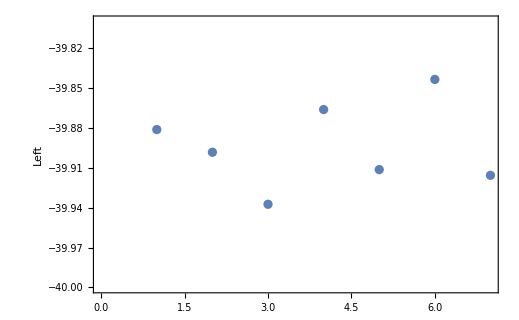

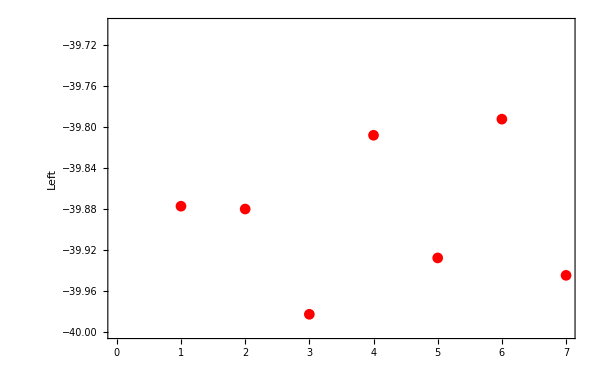

```mathematica
fig2=ListPlot[old,PlotStyle->Red,PlotRange->{Automatic,{-39.7,-40}},Frame->{{True,False},{True,False}},FrameTicks->{{Automatic,None},{Automatic,None}},FrameLabel->{{"Left","Right"},{None,None}}]
```

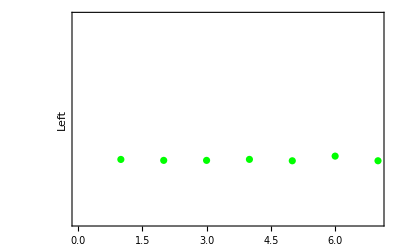

```mathematica
fig3=ListPlot[tot2,PlotStyle->Green,PlotRange->{Automatic,{-40,-39}},Frame->{{False, True},{True,False}},FrameTicks->{{None,Automatic},{Automatic,None}},FrameLabel->{{"Left","Right"},{None,None}}]
```

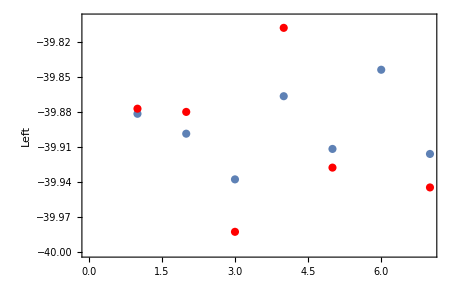

```mathematica
Show[fig1,fig2,fig3]
```

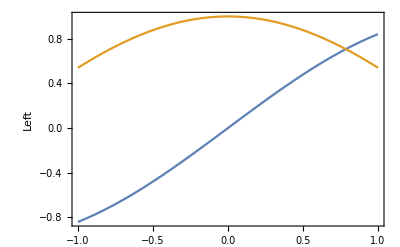

```mathematica
Plot[{Sin[x],Cos[x]},{x,-1,1},Frame->{{True,True},{True,False}},FrameTicks->{{Automatic,{{-0.5,5},{0,10},{0.5,15}}},{Automatic,None}},FrameLabel->{{"Left","Right"},{None,None}}]
```

```mathematica
new
```

{-39.8813,-39.8984,-39.9375,-39.8663,-39.9114,-39.8437,-39.9157}

```mathematica
old
```

{-39.877,-39.8797,-39.9824,-39.8078,-39.9274,-39.7921,-39.9444}

```mathematica
tot
```

{-472.703,-472.812,-472.813,-472.697,-472.86,-472.315,-472.858}

```mathematica
tot2
```

{-39.3919,-39.401,-39.4011,-39.3914,-39.405,-39.3596,-39.4048}

```mathematica
tot2=tot/5.5+46.06
```

{-39.886,-39.9059,-39.9061,-39.8848,-39.9146,-39.8155,-39.9142}

```mathematica
{-39.891924341666666,-39.901034966666664,-39.90111700833333,-39.8913825,-39.90500873333333,-39.859608316666666,-39.904827174999994}
```

```mathematica
fig1=ListLinePlot[{new,old,tot2},PlotRange->{{0.5,7.5},{-39.77,-40.02}},PlotStyle->{Automatic,Automatic,Dashed},PlotLegends->Placed[{"new","old","tot"},{1,0.8}],PlotMarkers->{●,●,●},Frame->{{True,True},{True,False}},FrameTicks->{{Automatic,{{-40,(-40-46.06)*5.5},{-39.9,(-39.9-46.06)*5.5},{-39.8,(-39.8-46.06)*5.5}}},{{{1,"6-31g(d,p)"},{2,"6-311g(d,p)"},{3,"6-311+g(d,p)"},{4,"cc-pvdz"},{5,"cc-pvtz"},{6,"def2-svp"},{7,"def2-tzvp"}},None}},FrameStyle->{{Directive[15],Directive[15]},{Directive[12],None}},RotateLabel->True,TicksStyle->Directive[Blue,18],FrameLabel->{{"Left","Right"},{None,None}}]
```

-Graphics-